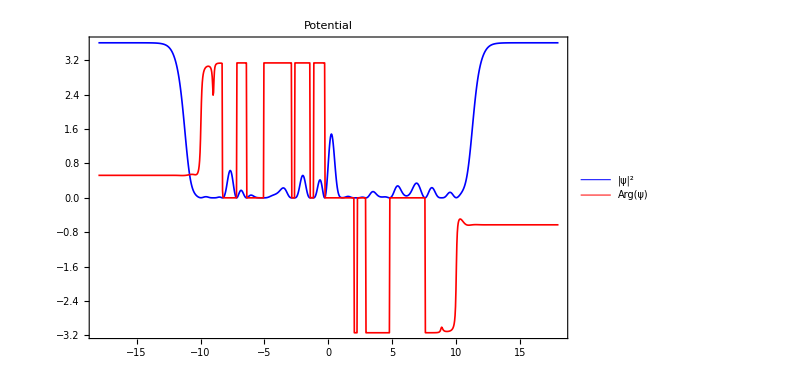

```mathematica
(* ::Title::*)(*Numerical Solution of the DST for a Composite Oscillatory Potential*)(* ::Text::*)(*This notebook sets up the spatial grid,defines the composite potential,and computes the left and right asymptotic phases required for the Discrete Spectrum Transform (DST).*)BeginPackage["DSTFunctions`"];

(* ::Section::*)
(*1. Simulation Parameters*)

(* ::Subsection::*)
(*1.1.Precision and Domain*)

precision=100;(*Working precision for arbitrary-precision arithmetic*)domainWidth=SetPrecision[36,precision];(*Physical width of the domain*)(* ::Subsection::*)(*1.2.Background Potential Parameters*)backgroundAmplitude=1.9;(*Amplitude of the asymptotic background potential*)leftPhase=SetPrecision[Pi/6,precision];(*Phase of the left asymptotic background*)rightPhase=SetPrecision[-Pi/5,precision];(*Phase of the right asymptotic background*)oscillatoryRegionHalfWidth=SetPrecision[22,100];(*Half-width of the central oscillatory region*)transitionWidth=0.7;(*Width parameter of the Tanh transitions*)(* ::Subsection::*)(*1.3.Discretization*)discretizationDegree=10;(*Grid-resolution parameter;number of points is 2^deg*)numPoints=2^discretizationDegree;

stepSize=domainWidth/numPoints;

integrationSteps=Table[stepSize,{i,numPoints}];

(* ::Section::*)
(*2. COMPOSITE POTENTIAL*)

(* ::Text::*)
(*The potential consists of two complex asymptotic plateaus connected by smooth Tanh transitions.A localized oscillatory perturbation is added near the center of the domain.*)

(*Piecewise potential,retained for reference*)

potentialExpression=N[Rationalize[backgroundAmplitude Exp[I leftPhase]*(1-Tanh[(x+oscillatoryRegionHalfWidth/2)/transitionWidth])/2+backgroundAmplitude Exp[I rightPhase]*(1+Tanh[(x-oscillatoryRegionHalfWidth/2)/transitionWidth])/2+(0.8 Sin[0.37 x]+0.6 Cos[0.89 x]+0.9 Sin[1.24 x]+0.4 Cos[1.76 x]+0.7 Sin[2.13 x]+0.5 Cos[2.58 x]+1.0 Sin[3.02 x]+0.3 Cos[3.47 x]+0.8 Sin[3.91 x]+0.6 Cos[4.36 x]+0.4 Sin[4.82 x]+0.9 Cos[2.29 x]+0.7 Sin[3.74 x]+0.5 Cos[4.18 x]+0.6 Sin[0.63 x]+0.8 Cos[1.07 x]+0.3 Sin[4.52 x]+0.7 Cos[0.96 x]+0.5 Sin[1.41 x]+0.9 Cos[4.87 x])*Exp[-(x/10)^8]*0.15,10^-12],precision];

compositePotential[t_?NumberQ]:=potentialExpression/.x->SetPrecision[t,precision];
(* ::Subsection::*)(*Randomly modulated hollow potential*)Clear[GenerateRandomPotential];

GenerateRandomPotential[variable_Symbol,amplitude_,thetaMinus_,thetaPlus_,separation_,sigma1_,sigma2_,modulation_,waveNumberRange_List,workingPrecision_Integer]:=Module[{sineCoefficients,cosineCoefficients,sineWaveNumbers,cosineWaveNumbers},sineCoefficients=RandomReal[{1/10,1},10,WorkingPrecision->workingPrecision];
cosineCoefficients=RandomReal[{1/10,1},10,WorkingPrecision->workingPrecision];
sineWaveNumbers=RandomReal[waveNumberRange,10,WorkingPrecision->workingPrecision];
cosineWaveNumbers=RandomReal[waveNumberRange,10,WorkingPrecision->workingPrecision];
N[amplitude Exp[I thetaMinus]*(1-Tanh[(variable+separation/2)/sigma1])/2+amplitude Exp[I thetaPlus]*(1+Tanh[(variable-separation/2)/sigma1])/2+modulation Exp[-(variable/sigma2)^8]*(Sum[sineCoefficients[[j]]*Sin[sineWaveNumbers[[j]] variable],{j,1,10}]+Sum[cosineCoefficients[[j]]*Cos[cosineWaveNumbers[[j]] variable],{j,1,10}]),workingPrecision]];


(*Parameters of the oscillatory addition*)

modulationAmplitude=N[15/100,precision];(*B*)localizationWidth=N[10,precision];(*sigma2*)waveNumberRange={3/10,5};






(* ::Section::*)
(*3. SPATIAL GRID AND ASYMPTOTIC PHASES*)

(* ::Subsection::*)
(*3.1.Spatial grid*)

spatialGrid=SetPrecision[Table[-domainWidth/2+stepSize (i-1)+stepSize/2,{i,1,numPoints}],precision];

(* ::Subsection::*)
(*3.2.Potential values on the grid*)

potentialData=SetPrecision[Table[compositePotential[spatialGrid[[i]]],{i,1,numPoints}],precision];

(* ::Subsection::*)
(*3.3.Asymptotic phases*)

phaseMinus=Arg[SetPrecision[potentialData[[1]],precision]];

phasePlus=Arg[SetPrecision[potentialData[[numPoints]],precision]];

(* ::Section::*)
(*4. VISUALIZATION*)

(* ::Subsection::*)
(*4.1.Plot of the composite potential magnitude and phase*)

potentialPlot=ListPlot[{Table[{spatialGrid[[i]],Abs[potentialData[[i]]]^2},{i,numPoints}],Table[{spatialGrid[[i]],Arg[potentialData[[i]]]},{i,numPoints}]},PlotRange->All,ImageSize->600,Frame->True,FrameLabel->{"",""},PlotLegends->{"|ψ|\!\(\*SuperscriptBox[\(\\ \), \(2\)]\)","Arg(ψ)"},PlotStyle->{{Blue,Thickness[0.002]},{Red,Thickness[0.002]}},Joined->True,PlotLabel->Style["Potential",14,Bold]];

potentialPlot
```

Root index | Approximate root | Refined root | ρ | log₂|ρ|
1 | -1.79636000735 | -1.79708282917 | 40640.3296685-55936.6149978 ⅈ | 16.0772634177
2 | -1.72650156262 | -1.72180151561 | 2.59406642276×10^6-(3.57042612479×10^6) ⅈ | 22.0734229236
3 | -1.61672400662 | -1.61441925237 | 3.31623403273×10^8-(4.56440456671×10^8) ⅈ | 29.0716095163
4 | -1.4470677837 | -1.44481436237 | 6.26221498465×10^9-(8.61919948698×10^9) ⅈ | 33.3106648248
5 | -1.31733067206 | -1.31400735167 | 3.52940808347×10^11-(4.85781347605×10^11) ⅈ | 39.1272742265
6 | -1.25745200515 | -1.25505783242 | 2.47349268169×10^12-(3.40447060749×10^12) ⅈ | 41.9363257027
7 | -1.03789689314 | -1.04138546847 | 1.25219790768×10^14-(1.72350256098×10^14) ⅈ | 47.5980948572
8 | -0.938099114951 | -0.942848128866 | 1.72188469725×10^14-(2.36997096643×10^14) ⅈ | 48.0576208001
9 | -0.838301336765 | -0.838891330361 | 5.02698863496×10^14-(6.91905627158×10^14) ⅈ | 49.6033266889
10 | -0.668645113848 | -0.670614863748 | 6.24990541809×10^13-(8.60225682211×10^13) ⅈ | 46.5955385238
11 | -0.369251779289 | -0.374070380396 | 2.23281519196×10^15-(3.07320646197×10^15) ⅈ | 51.7544242020
12 | -0.329332668015 | -0.324387305943 | 1.95709491676×10^16-(2.69371006008×10^16) ⅈ | 54.8862021779
13 | -0.159676445098 | -0.159087957245 | 8.76288713251×10^16-(1.20610794203×10^17) ⅈ | 57.0488947281
14 | -0.0399191112745 | -0.0369415589449 | 2.36082451382×10^16-(3.24939617822×10^16) ⅈ | 55.1567792576
15 | 0.079838222549 | 0.0770813442347 | 1.29267102980×10^16-(1.77920903453×10^16) ⅈ | 54.2878436235
16 | 0.239514667647 | 0.243361962855 | 6.73252469742×10^16-(9.26652527266×10^16) ⅈ | 56.6686360684
17 | 0.389211334927 | 0.389654966009 | 6.20198427632×10^16-(8.53629902898×10^16) ⅈ | 56.5502183196
18 | 0.469049557476 | 0.464323829261 | 8.39649723764×10^14-(1.15567869932×10^15) ⅈ | 50.3434198666
19 | 0.708564225123 | 0.704795435531 | 6.92293878650×10^13-(9.52860778227×10^13) ⅈ | 46.7430887583
20 | 0.858260892402 | 0.860288701946 | 2.59019399277×10^14-(3.56509618216×10^14) ⅈ | 48.6466924142
21 | 0.968038448407 | 0.971511788320 | 5.83134356462×10^13-(8.02615585440×10^13) ⅈ | 46.4955324910
22 | 1.09777556005 | 1.09494125105 | 5.41821910492×10^13-(7.45753881716×10^13) ⅈ | 46.3895229018
23 | 1.29737111642 | 1.30141656083 | 1.10311171572×10^12-(1.51830302177×10^12) ⅈ | 40.7713549765
24 | 1.36722956115 | 1.37014579824 | 1.35770726076×10^11-(1.86872372700×10^11) ⅈ | 37.7490204263
25 | 1.49696667279 | 1.49268083399 | 1.11676165048×10^9-(1.53709054519×10^9) ⅈ | 30.8233130925
26 | 1.65664311789 | 1.65168834681 | 3.94151729530×10^7-(5.42503314448×10^7) ⅈ | 25.9988867024
27 | 1.75644089608 | 1.75885876927 | 184098.943393-253390.457264 ⅈ | 18.2567607541
28 | 1.84625889645 | 1.85014385634 | 776.774389163-1069.13822553 ⅈ | 10.3679907577

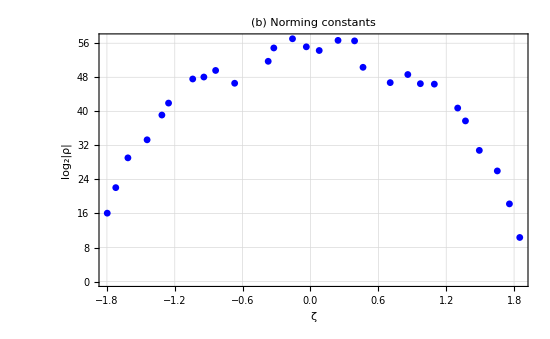

```mathematica
(* ::Section::*)(*5. Localization of Zeros and Calculation of Norming Constants*)(* ::Subsection::*)(*5.1.Numerical spectral function*)Clear[spectralA,spectralRealA];

spectralA[z_?NumericQ]:=SolitonDST`aDS[z,backgroundAmplitude,precision,potentialData,integrationSteps,numPoints,domainWidth,phaseMinus,phasePlus];

spectralRealA[z_?NumericQ]:=Re[spectralA[z]];


(* ::Subsection::*)
(*8.2.Search interval and spectral grid*)

zetaSearchMin=-backgroundAmplitude/(101/100);
zetaSearchMax=backgroundAmplitude/(101/100);
zetaSearchStep=1/100;

zetaSearchGrid=N[Subdivide[zetaSearchMin,zetaSearchMax,Ceiling[(zetaSearchMax-zetaSearchMin)/zetaSearchStep]],precision];

spectralSearchValues=spectralRealA/@zetaSearchGrid;

spectralSearchData=Transpose[{zetaSearchGrid,spectralSearchValues}];


(* ::Subsection::*)
(*5.3.Detect sign-change intervals and exact grid zeros*)

rootBrackets=Select[Partition[spectralSearchData,2,1],TrueQ[#[[1,2]] #[[2,2]]<0]&];

gridZeros=Cases[spectralSearchData,{z_,value_}/;TrueQ[value==0]:>z];

approximateBracketZeros=Mean[#[[All,1]]]&/@rootBrackets;

approximateZeros=Sort[Join[gridZeros,approximateBracketZeros]];


(* ::Subsection::*)
(*5.4.Refine each bracket using FindRoot*)

refinementResults=Table[Module[{left,right,start,root},left=rootBrackets[[i,1,1]];
right=rootBrackets[[i,2,1]];
start=(left+right)/2;
root=Check[zeta/.FindRoot[spectralRealA[zeta]==0,{zeta,left,right},Method->"Brent",WorkingPrecision->precision,MaxIterations->200],$Failed];
If[NumberQ[root],{start,root},Print["Root refinement failed in interval: ",{left,right}];
Nothing]],{i,Length[rootBrackets]}];

(*Columns:approximate root,refined root*)

rootPairs=SortBy[Join[({#,#}&/@gridZeros),refinementResults],Last];

matchedApproximateZeros=If[rootPairs==={},{},rootPairs[[All,1]]];

refinedZeros=If[rootPairs==={},{},rootPairs[[All,2]]];


(* ::Subsection::*)
(*5.5.Compute rho,its phase,and Log2[Abs[rho]]*)

rhoValues=Table[SolitonDST`RhoDS[refinedZeros[[i]],backgroundAmplitude,precision,potentialData,integrationSteps,numPoints,domainWidth,phaseMinus,phasePlus],{i,Length[refinedZeros]}];



log2AbsRho=Map[If[TrueQ[Abs[#]>0],Log[2,Abs[#]],Missing["ZeroOrNonNumericRho"]]&,rhoValues];


(* ::Subsection::*)(*5.6.Display the results table*)(*Columns:root index,approximate root,refined root,rho,Log2[Abs[rho]]*)rootResults=Table[{i,matchedApproximateZeros[[i]],refinedZeros[[i]],rhoValues[[i]],log2AbsRho[[i]]},{i,Length[refinedZeros]}];

Print[Grid[Prepend[Map[If[NumberQ[#],NumberForm[#,12],#]&,rootResults,{2}],{"Root index","Approximate root","Refined root","ρ","log₂|ρ|"}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}},Spacings->{2,1},ItemStyle->Directive[FontSize->12]]];


(* ::Section::*)
(*6. Visualization*)

(* ::Subsection::*)
(*6.1.Approximate and refined roots*)

(*Horizontal coordinate:root position.Vertical coordinate:root index.*)

approximateRootPlotData=Table[{matchedApproximateZeros[[i]],i},{i,Length[refinedZeros]}];

refinedRootPlotData=Table[{refinedZeros[[i]],i},{i,Length[refinedZeros]}];

rootsPlot=ListPlot[{approximateRootPlotData,refinedRootPlotData},Frame->True,Axes->False,FrameLabel->{Style["ζ",14],Style["Root index",14]},PlotStyle->{Blue,Red},PlotMarkers->{{"○",12},{"●",6}},Joined->False,PlotLegends->Placed[{"Approximate roots","Refined roots"},Below],PlotLabel->Style["(a) Approximate and refined roots",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.9]],PlotRange->All,ImageSize->550];


(* ::Subsection::*)
(*6.2.Log2 of the norming-constant modulus*)

logRhoPlotData=Cases[Transpose[{refinedZeros,log2AbsRho}],{z_?NumberQ,value_?NumberQ}];

rhoPlot=ListPlot[logRhoPlotData,Frame->True,Axes->False,FrameLabel->{Style["ζ",14],Style["log₂|ρ|",14]},PlotStyle->Directive[Blue,PointSize[0.012]],PlotMarkers->{"●",7},Joined->False,PlotLabel->Style["(b) Norming constants",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.9]],PlotRange->All,ImageSize->550];


(* ::Subsection::*)
(*6.3.Display both panels*)

GraphicsRow[{rootsPlot,rhoPlot},ImageSize->1200,Spacings->15]
```